Recurrence analysis of single particles (RASP)

Example datapaclet:Fretica/tutorial/RecurrenceAnalysisOfSingleParticlesRASP#205121859 | Recurrence histograms 1D&2Dpaclet:Fretica/tutorial/RecurrenceAnalysisOfSingleParticlesRASP#120250583
P_same(τ)paclet:Fretica/tutorial/RecurrenceAnalysisOfSingleParticlesRASP#567711402 |

Quantifying heterogeneity and conformational dynamics from single molecule FRET of diffusing molecules.

A. Hoffmann, et al. Phys. Chem. Chem. Phys., 2011,13, 1857-1871https://doi.org/10.1039/c0cp01911a

```mathematica
Needs["Fretica`"]
```

Example data

1

{2292.7,2831.6,49.0633,34.0889,0.,0.}

15673

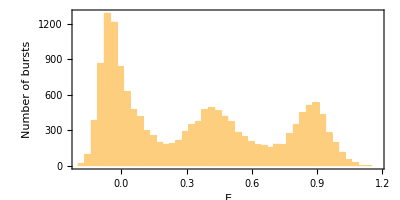

```mathematica
FEnablePie[False];
FSetFRETRoutes[{"A","D"}](* detector1: acceptor, detector2: donor*)
FSetRCM[{{1,-0.06},{-0.008,1.25}}];(*γ=1.25, Subscript[β, D->A]=0.06, Subscript[β, A->D]=0.008*)
FSetDirectAcceptorExcitation[0.05];


FOpenTTTR[$FreticaExamples<>"\\test.t3r"]
FDetermineBackground[]
FFindBurstsDeltaT[0.00015,30,10000]
FParamHisto["E",{-0.2,1.2,0.03}]
```

```mathematica
bl=FGetFromBurstList[{"E",1000.*"EndTime"}]ᵀ;
```

P_same(τ)

FSameMoleculeProbability calculates the probability that a molecule measured a time tau after a first measurement is still the same one, i.e. the molecule has "recurred".
The probability is given by 1-1/(G(τ))where G(τ) is the autocorrelation of the burst times.

```mathematica
?FSameMoleculeProbability
```

```mathematica
pl=FSameMoleculeProbability[{1,500},bl[[All,2]],PlotRange->{0,1}]
```

-Graphics-

```mathematica
PSdata=FSameMoleculeProbability[{1,500},bl[[All,2]],FOutput->FData]
```

{{1.,0.939439},{2.,0.936686},{3.,0.919514},{4.,0.901084},{5.,0.882526},{6.,0.869996},{7.,0.842009},{8.,0.817018},{9.,0.802739},{10.,0.776589},{12.,0.763424},{14.,0.723115},{16.,0.689057},{18.,0.657025},{20.,0.636957},{22.,0.603186},{24.,0.549492},{26.,0.486828},{28.,0.522714},{30.,0.493493},{34.,0.442843},{38.,0.38512},{42.,0.346875},{46.,0.320881},{50.,0.292731},{54.,0.279669},{58.,0.208681},{62.,0.281566},{66.,0.266117},{70.,0.265131},{78.,0.216633},{86.,0.212113},{94.,0.131949},{102.,0.161286},{110.,0.0823497},{118.,0.116504},{126.,0.157408},{134.,0.107846},{142.,0.100499},{150.,0.0690619},{166.,0.107855},{182.,0.0930393},{198.,0.101994},{214.,0.140857},{230.,0.110777},{246.,0.144901},{262.,0.0785178},{278.,-0.0330668},{294.,-0.0176577},{310.,0.0570471},{342.,0.0598969},{374.,0.0574708},{406.,0.0750442},{438.,0.0263927}}

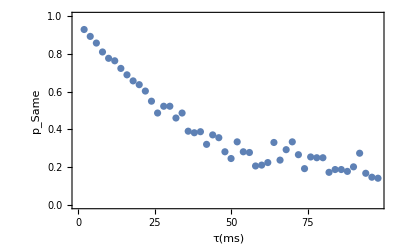

```mathematica
FSameMoleculeProbability[{2,100,2},bl[[All,2]],PlotRange->{0,1}]
```

```mathematica
FSameMoleculeProbability[{2,100,2},bl[[All,2]],FOutput->FData]
```

{{2.,0.929125},{4.,0.892601},{6.,0.857362},{8.,0.810147},{10.,0.776589},{12.,0.763424},{14.,0.723115},{16.,0.689057},{18.,0.657025},{20.,0.636957},{22.,0.603186},{24.,0.549492},{26.,0.486828},{28.,0.522714},{30.,0.522715},{32.,0.46046},{34.,0.486829},{36.,0.39061},{38.,0.382338},{40.,0.387878},{42.,0.32088},{44.,0.370953},{46.,0.356118},{48.,0.281563},{50.,0.245841},{52.,0.334133},{54.,0.281565},{56.,0.277764},{58.,0.20638},{60.,0.210968},{62.,0.224418},{64.,0.330871},{66.,0.237418},{68.,0.292735},{70.,0.334136},{72.,0.266118},{74.,0.192296},{76.,0.254088},{78.,0.24999},{80.,0.249991},{82.,0.172717},{84.,0.187491},{86.,0.187491},{88.,0.177702},{90.,0.201747},{92.,0.273929},{94.,0.167676},{96.,0.146868},{98.,0.141503}}

```mathematica
gtaumodel=Simplify[1+1/(Abs[nn] (1+t/Abs[τD])^(3/2))];
model=FullSimplify[1-1/gtaumodel]
```

Abs[τD]/(Abs[τD]+(Abs[nn] (t+Abs[τD])^(3/2))/(√Abs[τD]))

```mathematica
fitresult=FindFit[PSdata,model,{{τD,0.1},{nn,0.1}},{t}]
```

{τD→3.70567,nn→0.0383354}

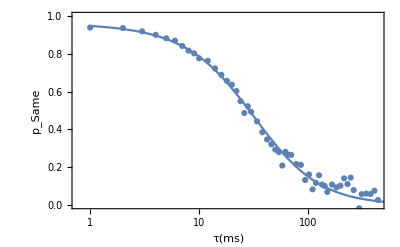

```mathematica
Show[pl,LogLinearPlot[Evaluate[model/.fitresult],{t,1,500}]]
```

Recurrence histograms 1D&2D

```mathematica
?FRecurrenceHisto
```

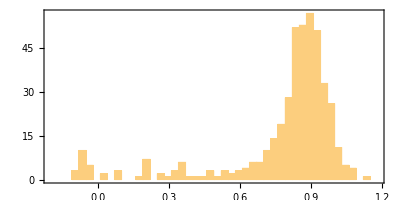

```mathematica
FRecurrenceHisto[bl,{0.9,1},{0,10},{-0.2,1.2,0.03}]
```

```mathematica
FRecurrenceHisto[bl,{0.9,1},{0,10},{-0.2,1.2,0.03},FOutput->FData]
```

{{-0.185,0,0.03},{-0.155,0,0.03},{-0.125,0,0.03},{-0.095,3,0.03},{-0.065,10,0.03},{-0.035,5,0.03},{-0.005,0,0.03},{0.025,2,0.03},{0.055,0,0.03},{0.085,3,0.03},{0.115,0,0.03},{0.145,0,0.03},{0.175,1,0.03},{0.205,7,0.03},{0.235,0,0.03},{0.265,2,0.03},{0.295,1,0.03},{0.325,3,0.03},{0.355,6,0.03},{0.385,1,0.03},{0.415,1,0.03},{0.445,1,0.03},{0.475,3,0.03},{0.505,1,0.03},{0.535,3,0.03},{0.565,2,0.03},{0.595,3,0.03},{0.625,4,0.03},{0.655,6,0.03},{0.685,6,0.03},{0.715,10,0.03},{0.745,14,0.03},{0.775,19,0.03},{0.805,28,0.03},{0.835,52,0.03},{0.865,53,0.03},{0.895,57,0.03},{0.925,51,0.03},{0.955,33,0.03},{0.985,26,0.03},{1.015,11,0.03},{1.045,5,0.03},{1.075,4,0.03},{1.105,0,0.03},{1.135,1,0.03},{1.165,0,0.03}}

```mathematica
?FRecurrenceHistoN
```

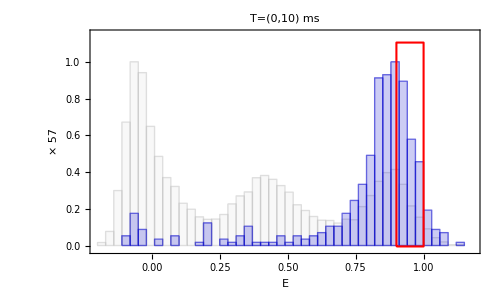

```mathematica
FRecurrenceHistoN[bl,{0.9,1},{0,10},{-0.2,1.2,0.03}]
```

```mathematica
Manipulate[
FRecurrenceHistoN[bl,{0.9,1},{0,dtmax},{-0.2,1.2,0.03}]
,{dtmax,1,200}]
```

```mathematica
Manipulate[FRecurrenceHistoN[bl,{e1,e1+0.05},{0,10},{-0.2,1.2,0.03}]
,{e1,-0.15,1.15,0.01}]
```

```mathematica
?FRecurrenceHisto2D
```

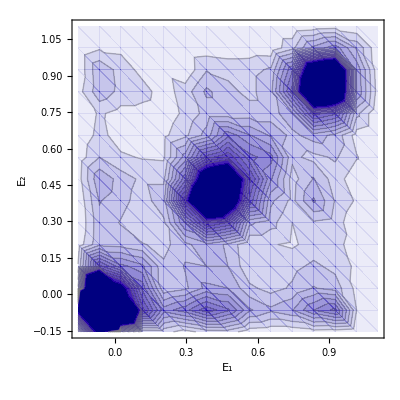

```mathematica
FRecurrenceHisto2D[bl,{0,40},{-0.2,1.2,0.09},PlotRange->{All,All,Automatic}]
```

| Related Guides
▪Fretica